# Lista 3 - Arthur Silva Magalhães

## 1. a)

Primeiramente vamos definir uma lista com as configurações visuais que serão utilizadas para o plot dos gráficos:

```mathematica
optam={ImageSize-> Large,LabelStyle-> Large};
```

Agora vamos definir os vetores e parâmetros do potencial dados na questão:

```mathematica
r1 = {-M2*R/(M1+M2),0};
r2 = {M1*R/(M1+M2),0};
r = {x,y};
ω = Sqrt[G*(M1+M2)/R^3];
```

Agora vamos definir o potencial tal como dado na questão:

```mathematica
V[x_,y_]:= -G*M1/(Norm[r-r1]) - G*M2/(Norm[r-r2])-ω^2*Norm[r]^2/2
```

Nos resta ainda definir alguns valores para as variáveis presentes no potencial, e também definir a relação entre as massas de que M2= M1/4:

```mathematica
pars = {M1->1,M2->1/4,G->1,R->1};
```

E então vamos traçar um gráfico em curvas de nível do potencial, mostrando os 5 pontos de Lagrange:

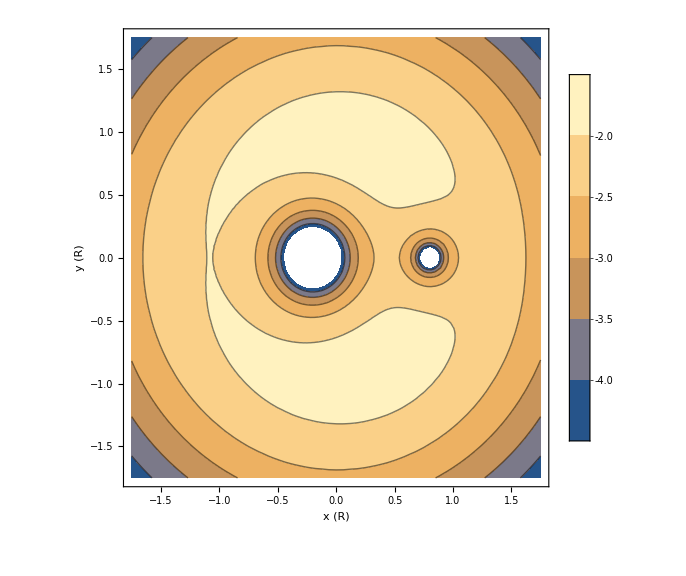

```mathematica
ContourPlot[V[x,y]/.pars,{x,-1.75,1.75},{y,-1.75,1.75},PlotLegends->Automatic,Evaluate[optam],FrameLabel-> {"x (R)","y (R)","V (GM1/R)"}]
```

Para podemos identificar mais claramente os pontos de Lagrange, colocarei um gráfico ilustrativo das curvas de nível do potencial com os 5 pontos de Lagrange demarcados. A imagem foi pode ser encontrada no link.

O ponto de Lagrange denotado por L2, que está localizado na parte exterior da órbita terrestre ao longo da reta que une a Terra e o Sol, é exatamente o ponto em que o Telescópio James Webb será instalado.

## b)

Vamos primeiramente definir novamente a equação do potencial, mas deste vez abrindo as normas e deixando explícito os parâmetros x e y (foi feito um teste com o potencial V da forma definida anteriormente e a função Solve demorava muito para ser computada ou dava erro):

```mathematica
V2[x_,y_]:= -G*M1/(Sqrt[(M2*R/(M1+M2)+x)^2+y^2])- G*M2/(Sqrt[(-M1*R/(M1+M2)+x)^2+y^2]) -  G*(M1+M2)/R^3* (x^2+y^2)/2
```

Agora vamos definir a força efetiva como sendo - o gradiente do potencial:

```mathematica
Fef = -Grad[V2[x,y],{x,y}]/.pars;
```

Agora vamos encontrar para quais pontos temos a força efetiva como 0:

```mathematica
Solve[{Fef[[1]]==0,Fef[[2]]==0},{x,y}]
```

{{x→Root1.27Root[-325+766 #1-505 #1^2+25 #1^3-750 #1^4+625 #1^5&,1]1.2710486907398812,y→0},{x→Root0.438Root[-315+866 #1-255 #1^2+25 #1^3-750 #1^4+625 #1^5&,1]0.438075958538366,y→0},{x→Root-1.08Root[325-734 #1+745 #1^2+25 #1^3-750 #1^4+625 #1^5&,1]-1.0828394642022434,y→0},{x→3/10,y→-(√3)/2},{x→3/10,y→(√3)/2}}

Vemos então que são exatamente os 5 pontos de Lagrange que enunciamos anteriormente. Vamos agora fazer um Plot duplo, juntando o gráfico das curvas de nível do potencial com o gráfico da lista dos pontos de Lagrange. Temos então:

```mathematica
P1 = ContourPlot[V2[x,y]/.pars,{x,-1.75,1.75},{y,-1.75,1.75},PlotLegends->Automatic,Evaluate[optam],FrameLabel-> {"x (R)","y (R)","V (GM1/R)"}];
```

```mathematica
P2 = ListPlot[{{Root"1.27"Root[-325+766 #1-505 #1^2+25 #1^3-750 #1^4+625 #1^5&,1]1.2710486907398812,0},{Root"0.438"Root[-315+866 #1-255 #1^2+25 #1^3-750 #1^4+625 #1^5&,1]0.438075958538366,0},{Root"-1.08"Root[325-734 #1+745 #1^2+25 #1^3-750 #1^4+625 #1^5&,1]-1.0828394642022434,0},{3/10,-(√3)/2},{3/10,(√3)/2}}];
```

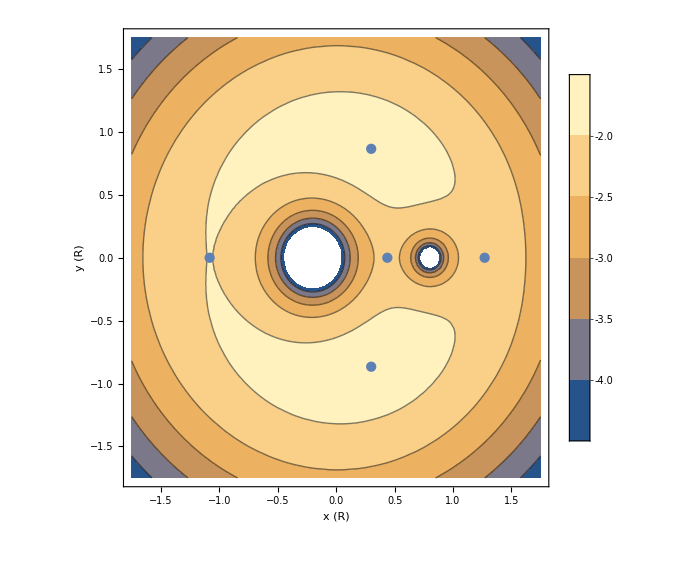

```mathematica
Show[P1,P2]
```

## c)

Primeiramente vamos fazer uma nova lista de substituições, em que a massa do Sol é dado por 1 e  a massa da terra é dado por 3*10^-6, que é e fração real da massa da Terra comparada com a do Sol.

```mathematica
pars2 = {M1->1,M2->3*10^-6,G->1,R->1};
```

Agora vamos encontrar os novos valores de força efetiva para este conjunto de parâmetros:

```mathematica
Fef2 = -Grad[V2[x,y],{x,y}]/.pars2;
```

Como feito anteriormente, vamos calcular os novos pontos de Lagrange do sistema, impondo o fato de que neles a força efetiva deve ser 0:

```mathematica
Solve[{Fef2[[1]]==0,Fef2[[2]]==0},{x,y}] //N
```

{{x→1.01003,y→0.},{x→0.99003,y→0.},{x→-1.,y→0.},{x→0.499997,y→-0.866025},{x→0.499997,y→0.866025}}

Como M1 >> M2, temos que a Terra está posicionada praticamente em (1,0), enquanto o Sol está em (0,0). Neste caso, podemos perceber que os pontos de Lagrange mais próximos da Terra são os dois primeiros encontrados na lista(L1 e L2). 

Como vimos anteriormente o James Webb estará orbitando o ponto L2, em {x→1.01003,y→0.}. Como a distância no gráfico está dada em termos de R, podemos encontrar o valor real da distância entre a Terra e o ponto L2 fazendo a conta (Posição do ponto L2 em x)*(Distância real Terra-Sol em Km) - (Distância Real Terra-Sol em Km). Desta forma conseguimos encontrar a distância real em Km entre Terra-L2. 

Como a distância Terra-Sol é 1.469 8 10^8 Km, temos então:

```mathematica
DistanciaTerraL2 = 1.496 * 10^8 * 1.010030218354984 -  1.496 * 10^8
```

1.50052×10^6

Podemos também encontrar a distância do outro ponto próximo a Terra (L1), utilizando este mesmo pensamento. Temos então:

```mathematica
DistanciaTerraL1 =   1.496 * 10^8 - 1.496 * 10^8 * 0.9900304472309229
```

1.49145×10^6

Vemos então que os pontos L1 e L2 próximos a Terra tem distâncias semelhantes de aproximadamente 1.5 *10^6 Km.

## 2. a)

Primeiramente vamos escrever o módulo do vetor campo elétrico fornecido, em termos de coordenadas cartesianas. Para isso utilizamos as transformações r = √(x^2+y^2+z^2) e θ = arctan(y/z).

```mathematica
eletricfield:= Abs[-A/Sqrt[x^2+y^2+z^2]*Sin[ArcTan[z,y]]*Cos[ω*(t-Sqrt[x^2+y^2+z^2]/c)]]
```

Agora vamos fazer as atribuições para os parâmetros independentes presentes na fórmula. Note que estamos fazendo x=0, para trabalharmos no plano yz, o que seria equivalente a fazer ϕ=π/2 em coordenadas esféricas.

```mathematica
optam={ImageSize-> Large,LabelStyle-> Large};
pa  = {A->1,c->1,ω->2*π,x->0}
```

{A→1,c→1,ω→2 π,x→0}

Agora vamos fazer a animação, com todas as configurações do modo que foram pedidas no enunciado, e também atribuindo o nome “gif” a ela para poder ser salva futuramente.

```mathematica
gif = Animate[DensityPlot[eletricfield /. pa /. {t->T},{y,-1,1},{z,-1,1}, Evaluate[optam], PlotLegends->BarLegend[{Automatic,{0,3}}], FrameLabel->{"y","z","E"},PlotPoints->100],{T,0,100},AnimationRate->24]
```

## b)

Agora vamos definir o diretório para ser salvo o gif e exportá-lo(se encontra anexado no moodle juntamente com o Notebook )

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["animado.gif",gif,"AnimationRepetitions"->∞,FrameRate->24]
```

animado.gif

## 3. a)

Primeiramente vamos  importar os dados para o Alumínio e para o chumbo:

```mathematica
optam={ImageSize-> Large,LabelStyle-> Large};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/arthurmaga/Workspace/lista3_fiscomp

```mathematica
dadosAl1 = Import["dados_Al.dat"];
```

```mathematica
dadosPb1 = Import["dados_Pb.dat"]
```

{{20,11.01},{40,19.57},{60,22.43},{80,23.69},{100,24.43},{150,25.27},{200,25.87},{250,26.36},{300,26.82}}

Agora vamos converter o calor específico por mol em calor específico por átomo. Assim vamos, para cada conjunto de dados, dividir as segunda coluna por R = K_b N_A= 8.31 J/K/mol:

```mathematica
dadosAl2 = Inner[Divide, dadosAl1,{1.,8.31}, List]
```

{{20.,0.0276775},{40.,0.251504},{60.,0.694344},{80.,1.16125},{100.,1.56919},{150.,2.22864},{200.,2.59687},{250.,2.79783},{300.,2.92659}}

```mathematica
dadosPb2 = Inner[Divide, dadosPb1,{1.,8.31}, List]
```

{{20.,1.32491},{40.,2.35499},{60.,2.69916},{80.,2.85078},{100.,2.93983},{150.,3.04091},{200.,3.11312},{250.,3.17208},{300.,3.22744}}

Dessa forma, vamos plotar o gráfico dos valores obtidos:

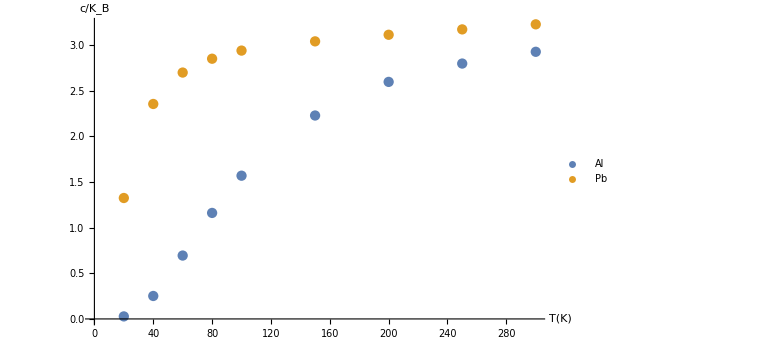

```mathematica
b1 = ListPlot[{dadosAl2, dadosPb2}, Evaluate[optam], PlotLegends->{"Al", "Pb"}, AxesLabel->{T[K], c/Subscript[K, B]}]
```

## b)

Vamos primeiramente escrever a fórmula do modelo de einstein u/K_B tal como dado no enunciado:

```mathematica
optam={ImageSize-> Large,LabelStyle-> Large};
```

```mathematica
EinsteinModel = 3/2 * (ℏ*ω/kb)*((Exp[ℏ*ω/(kb*T)]+1)/(Exp[ℏ*ω/(kb*T)]-1));
```

Vamos utilizar a relação dada de que , e então derivar a equação de einstein definida anteriormente em relação a T, para podermos encontrar uma função de c/K_Bpara ajustarmos aos dados experimentais.

```mathematica
c1 = D[EinsteinModel,T]/.{ℏ->1,kb->1} // FullSimplify
```

(3 ω^2 Csch[ω/(2 T)]^2)/(4 T^2)

Vamos fazer o ajuste para o alumínio e encontrar o valor de frequência ω que melhor ajusta (por mínimos quadrados) os seus dados experimentais:

```mathematica
FindFit[dadosAl2,c1,{{ω,100}},T]
```

{ω→276.714}

Agora vamos fazer o ajuste para o chumbo e encontrar o valor de frequência ω que melhor ajusta (por mínimos quadrados) os seus dados experimentais:

```mathematica
FindFit[dadosPb2 , c1,{{ω,20}},T]
```

{ω→65.5686}

Agora vamos fazer o plot do modelo de Einstein para cada conjunto de dados, para poder ver como a curva se comporta, e também para salvarmos os gráficos em variáveis que serão utilizadas posteriormente para a construção de um plot conjunto de todos os modelos e dados experimentais.

General::munfl: Csch[22575.7] is too small to represent as a normalized machine number; precision may be lost.

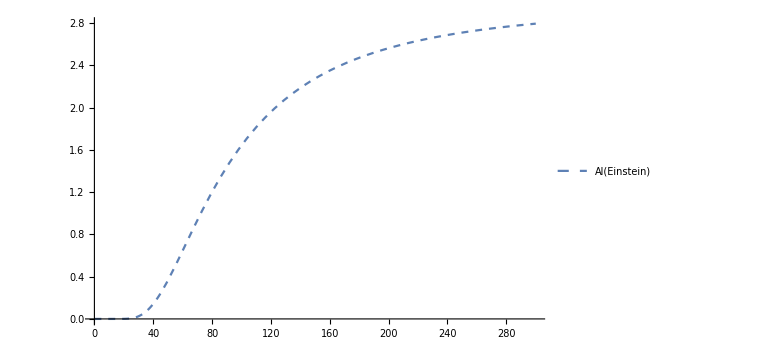

General::munfl: Csch[5349.42] is too small to represent as a normalized machine number; precision may be lost.

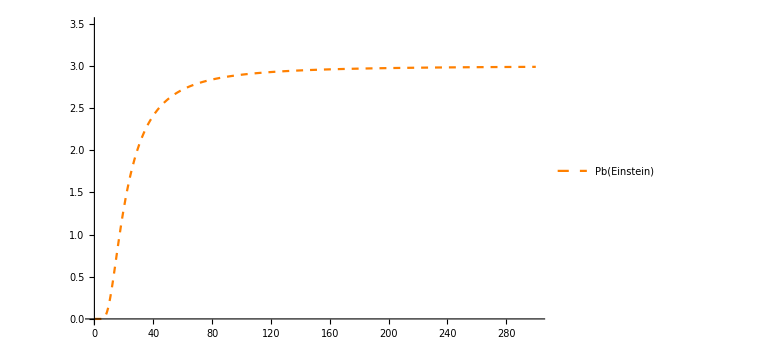

```mathematica
a1 = Plot[(3 ω^2 Csch[ω/(2 T)]^2)/(4 T^2)/.{ω->276.7141541632187},{T,0,300},PlotStyle->{Dashed},PlotLegends->{"Al(Einstein)"}, Evaluate[optam]]
a2 =  Plot[(3 ω^2 Csch[ω/(2 T)]^2)/(4 T^2)/.{ω->65.56861935809614},{T,0,300}, PlotStyle->{Orange,Dashed},PlotLegends->{"Pb(Einstein)"},Evaluate[optam],PlotRange->{0,3.5} ]
```

## c)

Primeiramente vamos definir o calor específico tal como dado pelo modelo de Debye:

```mathematica
c2 =Re[Assuming[ⅇ^(Td/T)⩽1, 9*kb*(T/Td)^3 *Integrate[(η^4*ⅇ^(η))/((ⅇ^(η)-1)^2),{η,0,Td/T}]]]/.{kb->1}
```

9 Re[1/Td^3 T^3 (-(4 π^4)/15+1/((-1+ⅇ^(Td/T)) T^4)(-ⅇ^(Td/T) Td^4-4 T Td^3 Log[1-ⅇ^(Td/T)]+4 ⅇ^(Td/T) T Td^3 Log[1-ⅇ^(Td/T)]+12 (-1+ⅇ^(Td/T)) T^2 Td^2 PolyLog[2,ⅇ^(Td/T)]-24 (-1+ⅇ^(Td/T)) T^3 Td PolyLog[3,ⅇ^(Td/T)]-24 T^4 PolyLog[4,ⅇ^(Td/T)]+24 ⅇ^(Td/T) T^4 PolyLog[4,ⅇ^(Td/T)]))]

Note que tomamos somente a parte real (com sentido físico), e também impomos a condição de que  para podermos ter o resultado sem as condicionais dadas pelo Mathematica.

Temos agora que encontrar o parâmetro    que melhor ajusta para cada manterial. Vamos chutar o valor tal como chutamos os valores de T_d tal como chutamos para o ω anteriormente:

```mathematica
FindFit[dadosAl2 , c2/.{kb->1},{{Td,100}},T]
```

{Td→378.439}

```mathematica
FindFit[dadosPb2 , c2/.{kb->1},{{Td,20}},T]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Td→88.0273}

Agora novamente vamos fazer os plots para cada material, utilizando o valor do parâmetro encontrado.

General::munfl: 7.08864×10^8 2.1121925902×10^-26818 is too small to represent as a normalized machine number; precision may be lost.

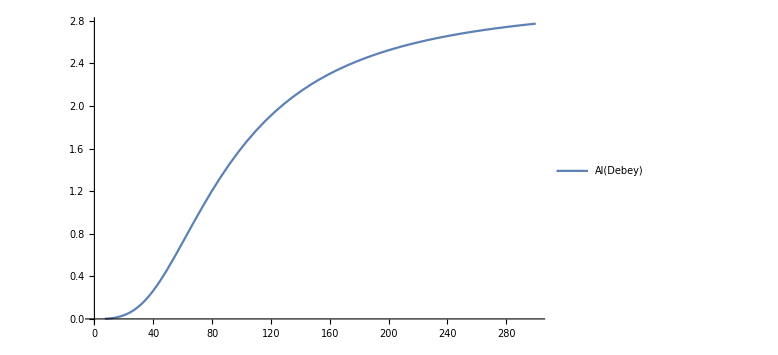

```mathematica
a3 =  Plot[c2/.{kb->1, Td-> 378.43915883670275},{T,0,300},PlotLegends->{"Al(Debey)"}, Evaluate[optam]]
```

General::munfl: 7.08864×10^8 1.0977771643×10^-6238 is too small to represent as a normalized machine number; precision may be lost.

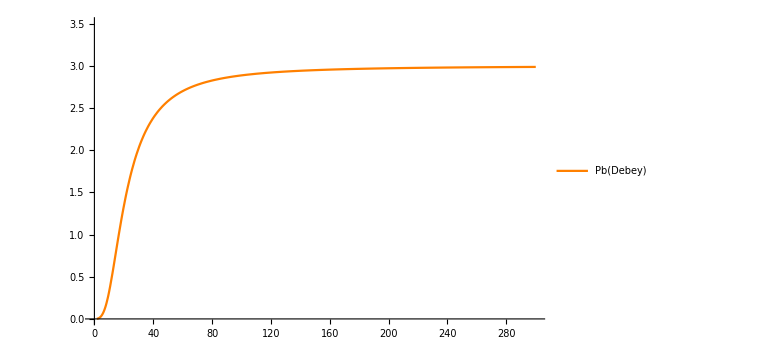

```mathematica
a4 =  Plot[c2/.{kb->1, Td->88.02732217496332},{T,0,300},PlotStyle->Orange,PlotLegends->{"Pb(Debey)"},Evaluate[optam],PlotRange->{0,3.5}]
```

## d)

Finalmente vamos evocar a função Show[] e plotar todos os gráficos juntos.

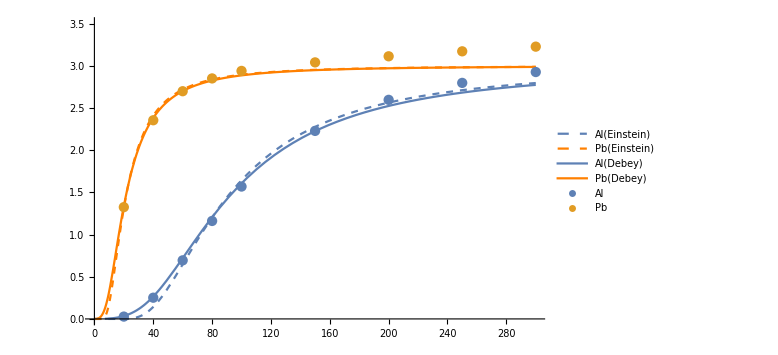

```mathematica
Show[a1,a2,a3,a4,b1, Evaluate[optam], PlotRange->{{0,300},{0,3.5}},PlotLegends->"Expressions",Exclusions->None]
```

Podemos ver que o modelo de Debye é mais preciso em temperaturas mais baixas, enquanto ambos os modelos são semelhantes para temperaturas altas.

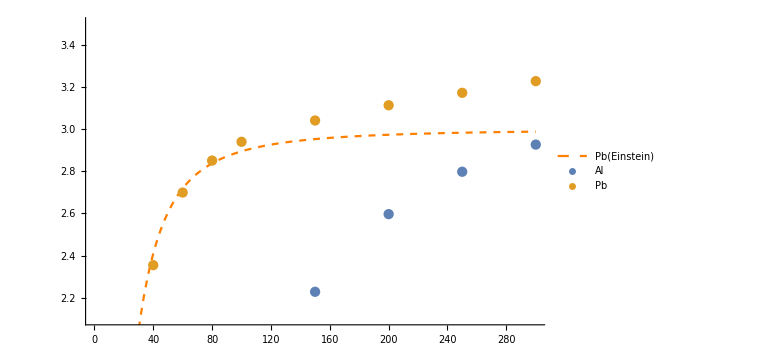

```mathematica
Show[a2,b1, PlotRange->{{0,300},{2.1,3.5}}]
```